```mathematica
ParticleTimeSeries[d_,n_]:=
Module[
{dir=d, name=n},
file=dir<>"/txt_stack/"<>name<>".txt";
particles=Import[file,"Table"];
nparticles=Differences[Position[particles,"t",2]][[1,1]]-1;
dt=particles[[2+nparticles,3]];
particlesT=Partition[particles[[2;;]],nparticles, nparticles+1];
{nparticles, dt,particlesT}
];

MSD[d_,n_,nl_]:=
Module[
{dir=d, name=n,nlags=nl},
{nparticles,dt,particlesT} = ParticleTimeSeries[dir, name];
nt=Length[particlesT];
msds = Table[
{
lag*dt,
Mean[
Flatten[
Table[
(particlesT[[t+lag,All,1]]-particlesT[[t,All,1]])^2 + (particlesT[[t+lag,All,2]]-particlesT[[t,All,2]])^2,
{t,1,nt-lag}
]
]
]},
{lag,1,nt,Floor[nt/nlags]}
];
msds
];
```

```mathematica
mdwout = "/Volumes/homes/Code/cytomod/shila/semiflexible/out/network/";
```

## Different dts

```mathematica
dts={".00001",".00004",".00007",".00010",".00040",".00070",".00100",".00400",".00700",".01000"};
dtdirs = Table["sticky_clnk_rigid_dt"<>dt,{dt,dts}];
```

```mathematica
dtmsds=Table[MSD[mdwout<>dtdir,"rods",100],{dtdir, dtdirs}];
```

```mathematica
dtmsd1=MSD[mdwout<>dtdirs[[1]],"rods",100];
```

```mathematica
dtmsds=Insert[dtmsds,dtmsd1,1];
```

```mathematica
Length[dtmsds]
```

10

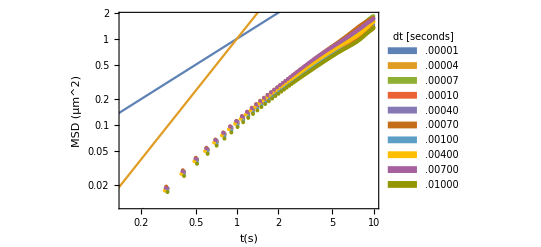

```mathematica
Show[
ListLogLogPlot[dtmsds,Frame->True, FrameLabel->{"t(s)","MSD (μm^2)","Mean Squared Displacement for varying dt"},PlotLegends->SwatchLegend[dts,LegendLabel->"dt [seconds]",LegendFunction->(Framed[#,Background->LightBlue]&)]]
,LogLogPlot[{x,x^2},{x,0.01,10}]]
```

```mathematica
logdtmsds = Log[dtmsds];
```

```mathematica
InterpFs=
Table[
ListInterpolation[logdtmsds[[i,All,2]],dtmsds[[i,All,1]]],
{i,1,Length[dts]}
];
```

```mathematica
errs=
Table[
Transpose[
{dtmsds[[1,2;;-2,1]],
Abs[
Map[InterpFs[[k-1]],dtmsds[[1,2;;-2,1]]]-logdtmsds[[1,2;;-2,2]]
]/logdtmsds[[1,2;;-2,2]]*100
}
],
{k,2,Length[dts]}
];
```

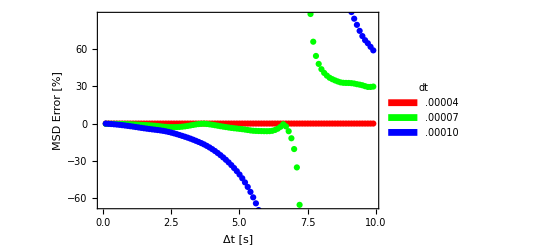

```mathematica
ListPlot[errs[[1;;3]],Frame->True,PlotStyle->{Red,Green,Blue},FrameLabel->{"Δt [s]","MSD Error [%]","Mean Squared Displacement Error (from dt = 1e-5) for dt = O(1e-4)"},PlotLegends->SwatchLegend[{Red,Green,Blue},dts[[2;;4]],LegendLabel->"dt",LegendFunction->(Framed[#,Background->LightBlue]&)],BaseStyle->{FontSize->14}
]
```

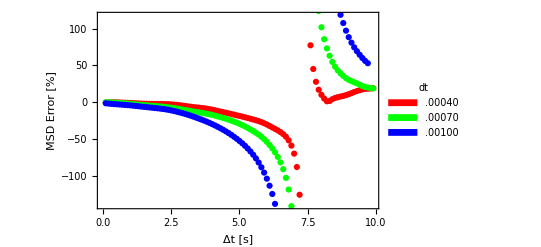

```mathematica
ListPlot[errs[[4;;6]],Frame->True,PlotStyle->{Red,Green,Blue},FrameLabel->{"Δt [s]","MSD Error [%]","Mean Squared Displacement Error (from dt = 1e-5) for dt = O(1e-3)"},PlotLegends->SwatchLegend[{Red,Green,Blue},dts[[5;;7]],LegendLabel->"dt",LegendFunction->(Framed[#,Background->LightBlue]&)],BaseStyle->{FontSize->14}
]
```

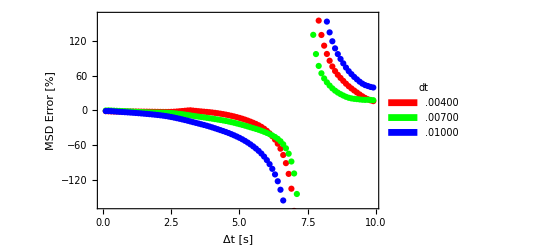

```mathematica
ListPlot[errs[[7;;9]],Frame->True,PlotStyle->{Red,Green,Blue},FrameLabel->{"Δt [s]","MSD Error [%]","Mean Squared Displacement Error (from dt = 1e-5) for dt = O(1e-2)"},PlotLegends->SwatchLegend[{Red,Green,Blue},dts[[8;;10]],LegendLabel->"dt",LegendFunction->(Framed[#,Background->LightBlue]&)],BaseStyle->{FontSize->14}
]
```

## dt = 1 e - 5, different seeds

```mathematica
seeds=Catenate[{{"1"},Table[ToString[Prime[i]],{i,12}]}]
```

{1,2,3,5,7,11,13,17,19,23,29,31,37}

```mathematica
seedDirs = Table[mdwout<>"sticky_clnk_rigid_seed"<>seed,{seed,seeds}];
```

```mathematica
msds=Table[MSD[seedDir,"rods",100],{seedDir,seedDirs}];
```

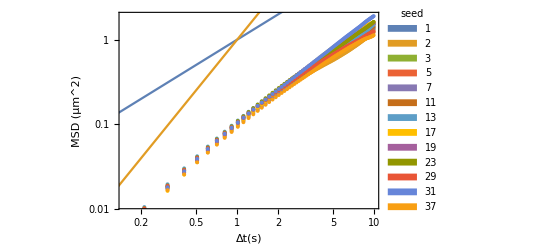

```mathematica
Show[ListLogLogPlot[msds,Frame->True, FrameLabel->{"Δt(s)","MSD (μm^2)","Mean Squared Displacement for varying Seeds"},PlotLegends->SwatchLegend[seeds,LegendLabel->"seed",LegendFunction->(Framed[#,Background->LightBlue]&)]],LogLogPlot[{x,x^2},{x,0.01,10}]]
```

```mathematica
msds[[1,-2,2]]
```

1.53134

```mathematica
mlasterrs=Catenate[Table[Abs[msds[[i,-2,2]]-msds[[j,-2,2]]]/msds[[j,-2,2]],{i,1,Length[msds]},{j,i+1,Length[msds]}]]
```

{0.260766,0.159824,0.00912514,0.111143,0.0737841,0.0154754,0.0450557,0.0321517,0.0565616,0.220386,0.19225,0.358615,0.0800644,0.199594,0.118677,0.148308,0.194557,0.242568,0.232333,0.251694,0.0320285,0.359318,0.0776108,0.129932,0.0419728,0.0741833,0.124457,0.176647,0.165521,0.186567,0.0522166,0.303558,0.171398,0.101095,0.0640743,0.00629287,0.0536909,0.0409036,0.0650928,0.20935,0.199554,0.34633,0.0336217,0.086098,0.140574,0.128961,0.15093,0.098316,0.273046,0.222719,0.054302,0.110674,0.0986565,0.121389,0.136528,0.247754,0.265259,0.0596086,0.0469013,0.0709392,0.201788,0.20456,0.337911,0.0135128,0.0120488,0.277965,0.154139,0.422717,0.0252208,0.260927,0.165417,0.403748,0.293551,0.143823,0.440068,0.338119,0.113267,0.681975}

```mathematica
Mean[mlasterrs]
```

0.164382

```mathematica
StandardDeviation[mlasterrs]
```

0.123371

## Experiments

```mathematica
{nparticles,dt,particlesT} = ParticleTimeSeries[seedDirs[[1]], "rods"];
```

```mathematica
Length[particlesT[[1,1]]]
```

4

```mathematica
rodps = particlesT[[All,All,1;;2]];
```

```mathematica
u=rodps[[1,1;;4]];v=rodps[[2,1;;4]];
```

```mathematica
u
```

{{-5.,0.},{5.80887,1.04997},{-10.5719,17.1196},{-4.11553,3.74674}}

```mathematica
v
```

{{-5.0096,-0.004994},{5.80372,1.04547},{-10.5786,17.1116},{-4.11066,3.75172}}

```mathematica
Table[EuclideanDistance[u[[i]],v[[i]]],{i,Length[v]}]
```

{0.0108239,0.00683104,0.0104797,0.00695976}

```mathematica
Clear[g]
```

```mathematica
g[{u_,v_}]:=EuclideanDistance[u,v];
```

```mathematica
Thread[g[u,v]]
```

0.0176813

```mathematica
Map[g,Transpose[{u,v}]]
```

{0.0108239,0.00683104,0.0104797,0.00695976}

```mathematica
Table[EuclideanDistance[u[[i]],v[[i]]],{i,Length[v]}]//AbsoluteTiming
```

{0.00003,{0.0108239,0.00683104,0.0104797,0.00695976}}

```mathematica
Map[g,Transpose[{u,v}]]//AbsoluteTiming
```

{0.00004,{0.0108239,0.00683104,0.0104797,0.00695976}}

```mathematica
kk=rodps[[1,All]];jj=rodps[[2,All]];
```

```mathematica
Table[EuclideanDistance[kk[[i]],kk[[i]]],{i,Length[jj]}];//AbsoluteTiming
```

{0.00141,Null}

```mathematica
Map[g,Transpose[{kk,jj}]];//AbsoluteTiming
```

{0.00139,Null}

```mathematica
Sqrt[(v[[All,1]]-u[[All,1]])^2+(v[[All,2]]-u[[All,2]])^2];//AbsoluteTiming
```

{0.00003,Null}

```mathematica
Sqrt[(kk[[All,1]]-jj[[All,1]])^2+(kk[[All,2]]-jj[[All,2]])^2];//AbsoluteTiming
```

{0.00024,Null}

```mathematica
Sqrt[(v-u)^2]
```

{{0.009603,0.004994},{0.005142,0.004497},{0.006705,0.008054},{0.004867,0.004975}}

```mathematica
ll=Table[
(particlesT[[t+5,All,1]]-particlesT[[t,All,1]])^2 + (particlesT[[t+5,All,2]]-particlesT[[t,All,2]])^2,
{t,1,nt-5}
];
```

```mathematica
Length[ll[[1]]]
```

500

```mathematica
yy=Catenate[ll];
```

```mathematica
Length[yy]
```

498000

```mathematica
Length[ll[[1]]]*Length[ll]
```

498000

```mathematica
Mean[yy]
```

0.00103855

```mathematica
yy==ll
```

False

```mathematica
Catenate[ll];//AbsoluteTiming
```

{0.00258,Null}

```mathematica
Flatten[ll];//AbsoluteTiming
```

{0.00254,Null}

```mathematica
Flatten[ll]==Catenate[ll]
```

True